# Confocal Fiber Microscopy Resolution

Image formation in a fiber-optical confocal scanning microscope. Gu, Min Sheppard, C J R Gan, X

### Dimmensionless Confocal Parameter

```mathematica
A=16;
```

### Transversal Resolution

```mathematica
Subscript[ρ, o][l_,θ_]=√(1+l^2(Sin[(θ/4)])^2)-(l Cos[θ])/2; (* Eq (22) *)
```

```mathematica
cCSM[l_]=2/(π(1−Exp[−A]))Exp[(−A l^2)/4]×NIntegrate[1−Exp[−A(Subscript[ρ, o][l,θ])^2],{θ,0,π/2}]; (* Eq (21) *)
cconf[l_]= 2/π((ArcCos[l/2])-l/2 √(1-(l/2)^2));
cnorm[l_]= 2/π((ArcCos[l])-l √(1-l^2));
```

NIntegrate::inumr: The integrand 1-ⅇ^(-16 (-1/2 l Cos[«1»]+√Plus[«2»])^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.5708}}.

```mathematica
csmMTF = Transpose[{Range[0,2,0.01],cCSM[Range[0,2,0.01]]}];
confMTF = Transpose[{Range[0,2,0.01],cconf[Range[0,2,0.01]]}];
cnormMTF = Transpose[{Range[0,2,0.01],cnorm[Range[0,2,0.01]]}];
```

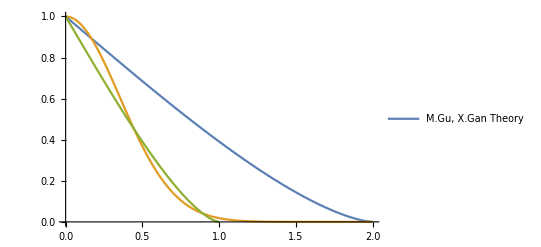

```mathematica
ListLinePlot[{confMTF,csmMTF, cnormMTF},PlotLegends->{"M.Gu, X.Gan Theory"},PlotRange->{{0,2},{0,1}}]
```

```mathematica
Export["csmMTF.csv",csmMTF]
```

csmMTF.csv

```mathematica
Export["confMTF.csv",confMTF]
```

confMTF.csv

```mathematica
Export["cnormMTF.csv",cnormMTF]
```

cnormMTF.csv